# Estimating the Age of The Universe.

Submitted by: Islam Alaa Fathallah

Based on data from observed supernovae using the Hubble Space Telescope and calculations made to estimate their recessional velocities and distances from us, as provided in the following research paper:

“Freedman, W. L., Madore, B. F., Gibson, B. K., Ferrarese, L., Kelson, D. D., Sakai, S., Mould, J. R., Kennicutt, R. C., Jr., Ford, H. C., & Graham, J. A. (2001). Final Results from the Hubble Space Telescope Key Project to Measure the Hubble Constant. The Astrophysical Journal, 553(1), 47. DOI: 10.1086/320638.”  

                                                                          -Graphics-
We use the data presented in Table 6 to construct the Hubble plot and fit it to determine the Hubble constant, which can then be used to estimate the age of the universe.

## 1. Data Processing

Import the data from the csv file

```mathematica
data = Import["D:\\Mathematica\\Project\\Data.csv"];
TableForm[data]
```

Supernova | V(km/s) | D(Mpc)
SN 1990O... | 9065 | 134.7
SN 1990T... | 12012 | 158.9
SN 1990af... | 15055 | 198.6
SN 1991S... | 16687 | 238.9
SN 1991U... | 9801 | 117.1
SN 1991ag... | 4124 | 56
SN 1992J... | 13707 | 183.9
SN 1992P... | 7880 | 121.5
SN 1992ae... | 22426 | 274.6
SN 1992ag... | 7765 | 102.1
SN 1992al... | 4227 | 58
SN 1992aq... | 30253 | 467
SN 1992au... | 18212 | 262.2
SN 1992bc... | 5935 | 88.6
SN 1992bg... | 10696 | 151.4
SN 1992bh... | 13518 | 202.5
SN 1992bk... | 17371 | 235.9
SN 1992bl... | 12871 | 176.8
SN 1992bo... | 5434 | 77.9
SN 1992bp... | 23646 | 309.5
SN 1992br... | 26318 | 391.5
SN 1992bs... | 18997 | 280.1
SN 1993B... | 21190 | 303.4
SN 1993O... | 15567 | 236.1
SN 1993ag... | 15002 | 215.4
SN 1993ah... | 8604 | 119.7
SN 1993ac... | 14764 | 202.3
SN 1993ae... | 5424 | 71.8
SN 1994M... | 7241 | 96.7
SN 1994Q... | 8691 | 127.8
SN 1994S... | 4847 | 66.8
SN 1994T... | 10715 | 149.9
SN 1995ac... | 14634 | 185.6
SN 1995ak... | 6673 | 82.4
SN 1996C... | 9024 | 136
SN 1996bl... | 10446 | 132.7

Determine the length of the table

```mathematica
length =Length[data]
```

37

Extract the distance and velocity from the table

```mathematica
r=data[[2;;,3]]
v= data[[2;;,2]]
```

{134.7,158.9,198.6,238.9,117.1,56,183.9,121.5,274.6,102.1,58,467,262.2,88.6,151.4,202.5,235.9,176.8,77.9,309.5,391.5,280.1,303.4,236.1,215.4,119.7,202.3,71.8,96.7,127.8,66.8,149.9,185.6,82.4,136,132.7}

{9065,12012,15055,16687,9801,4124,13707,7880,22426,7765,4227,30253,18212,5935,10696,13518,17371,12871,5434,23646,26318,18997,21190,15567,15002,8604,14764,5424,7241,8691,4847,10715,14634,6673,9024,10446}

Making a set of Coordinates (r,v)

```mathematica
coord ={r,v}//Transpose
```

{{134.7,9065},{158.9,12012},{198.6,15055},{238.9,16687},{117.1,9801},{56,4124},{183.9,13707},{121.5,7880},{274.6,22426},{102.1,7765},{58,4227},{467,30253},{262.2,18212},{88.6,5935},{151.4,10696},{202.5,13518},{235.9,17371},{176.8,12871},{77.9,5434},{309.5,23646},{391.5,26318},{280.1,18997},{303.4,21190},{236.1,15567},{215.4,15002},{119.7,8604},{202.3,14764},{71.8,5424},{96.7,7241},{127.8,8691},{66.8,4847},{149.9,10715},{185.6,14634},{82.4,6673},{136,9024},{132.7,10446}}

Plot the set of coordinates

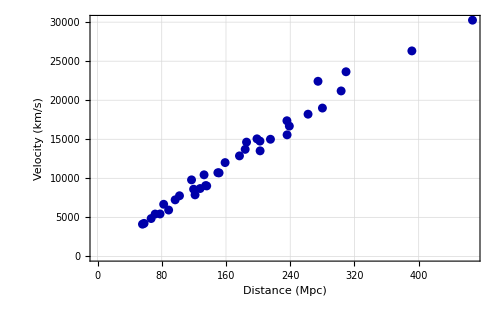

```mathematica
plot =ListPlot[coord,PlotStyle->Darker[Blue],GridLines->Automatic,Frame->True,FrameStyle->Directive[Black,15],FrameLabel->{"Distance (Mpc)","Velocity (km/s)"},ImageSize->500]
```

### 2. Correlation Factor

R = ((n∑_(i=1)^n X_i y_i)-(∑_(i=1)^n X_i) (∑_(i=1)^n y_i))/(√((n∑_(i=1)^n X_i^2)-(∑_(i=1)^n X_i)^2) √((n∑_(i=1)^n y_i^2)-(∑_(i=1)^n y_i)^2))

This formula computes the correlation coefficient between two variables X and y providing a measure of the strength and direction of their linear relationship . The coefficient R ranges between - 1 and 1:

R = 1 implies a perfect positive linear relationship,
R = −1 implies a perfect negative linear relationship, and
R = 0 implies no linear relationship between the variables .

```mathematica
corr = Correlation[r,v]
```

0.989079

So, based on the previous value of R we can use the linear fitting model

### 3. Regression Line

```mathematica
lmf=LinearModelFit[coord,x,x,IncludeConstantBasis->False]
```

FittedModel[70.6672 x]

```mathematica
regline= Normal[lmf]
```

70.6672 x

```mathematica
H = 70.6672 (*(km/s)/Mpc*);
```

Based on the hubble’s formula: v = H.D
where, v: the recessional velocity (km/s) , H: hubble’s constant ((km/s)/Mpc), D: distance (Mpc)
Then, from the previous fitting line, the hubble’s constant, H =  70.6672 (km/s)/Mpc

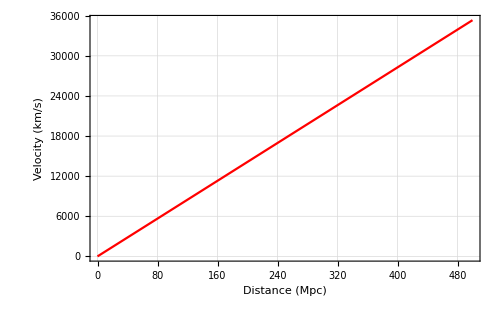

```mathematica
lmfp=Plot[regline,{x,0,500},PlotStyle->Red,GridLines->Automatic,Frame->True,FrameStyle->Directive[Black,15],FrameLabel->{"Distance (Mpc)","Velocity (km/s)"},ImageSize->500]
```

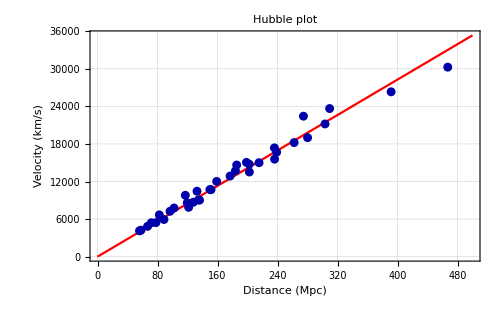

```mathematica
Show[{lmfp,plot},PlotLabel->HoldForm[Hubble plot],LabelStyle->{14,GrayLevel[0],Bold}]
```

## 4. Final Report

Based on the previous calculation we can get the age of the universe  t = 1/H_0

```mathematica
MpcToKilometers=3.09*10^19; (*Conversion factor:1 Mpc=3.09 x 10^19 km*)
SecondsInYear=3.15*10^7;
Subscript[t, age]= 1/H *MpcToKilometers/SecondsInYear
```

1.38813×10^10

From the previous calculations, we estimated that, the age of the universe is about 13.8813 billion year